{{{0.683253,0.126203},{0.364452,0.135822},{0.0331702,0.212673},{0.331624,0.435284},{0.603292,0.524709},{0.821279,0.585854},{0.992018,0.719507},{0.640159,0.772129},{0.0353583,0.93335},{0.226484,0.936777}},CSMinkowski2Rectangle,2,10,1,{1,1}}

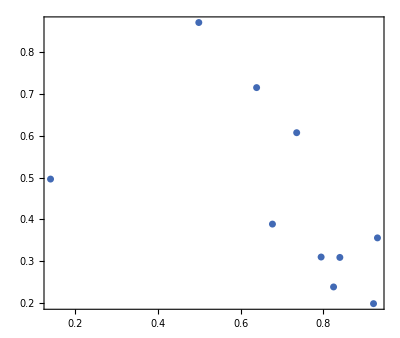

```mathematica
ρ:=10
m:=30
A:=CSMinkowski2Rectangle[1,1,ρ]
Subscript[C, 1]:=CausalMatrix[A]
A
L:=LinkMatrix[A]
CPlot[A]
```

```mathematica
K:=1/2 Subscript[C, 1].Inverse[IdentityMatrix[ρ]+m^2/(2ρ)Subscript[C, 1]]
MatrixForm[K]
```

(0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2 | 1/2 | -45/2
0 | 0 | 0 | 1/2 | 0 | 0 | 1/2 | 1/2 | -22 | -22
0 | 0 | 0 | 0 | 1/2 | -22 | -45/2 | 1/2 | 0 | 3961/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)